### Metropolis sampling of a quarterly sales distribution

Set up the quarterly data. Define functions that make the quarter “to the left of” Q1 be Q4, and the quarter “to the right of” Q4 be Q1. Choose the initial position for the algorithm and normalize the sales.

```mathematica
unitSalesByQuarterInMillions={
{"Q1",25},
{"Q2",50},
{"Q3",100},
{"Q4",75}
};
annualUnitSales=Total[unitSalesByQuarterInMillions]⟦2⟧;
wrapUpper[n_]:=If[n≤4,n,1]
wrapLower[n_]:=If[n≥1,n,4]
wrap[n_]:=wrapUpper[wrapLower[n]]
position=RandomInteger[{1,4}];
normalizedUnitSales=N[unitSalesByQuarterInMillions⟦All,2⟧/=annualUnitSales]
```

{0.1,0.2,0.4,0.3}

Then we run the algorithm 125 times and accumulate the samples.

Andy, the code that follows feels procedural rather than functional. I am hoping you can help me think differently. The ratio is a simplified Metropolis algorithm. I could alter it a bit to make it the standard algorithm, but that isn’t the issue. The issue is that I still don’t have the hang of programming functionally. Pointers would be very welcome. ~Brian

```mathematica
accumulator=ConstantArray[0,4];
iterations=125;
(* Next we initialize explorations which is a bunch of left and right movements. In Metropolis you propose a movement randomly, and then you evaluate a ratio to decide whether you accept the proposal. *)
explorations=RandomInteger[{0,1},iterations]*2-1;

accumulate[z_]:=(newPosition=wrap[position+z];
ratio=normalizedUnitSales⟦newPosition⟧/(normalizedUnitSales⟦newPosition⟧+normalizedUnitSales⟦position⟧);
position=If[RandomReal[]<ratio,newPosition,position];
accumulator⟦position⟧+=1;)

Map[accumulate,explorations];
```

Finally we plot what we accumulated (orange) next to the expected values from the original distribution (blue).

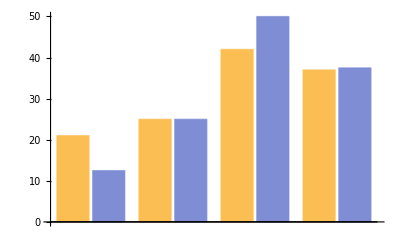

```mathematica
expected=normalizedUnitSales*iterations;
BarChart[Transpose[{accumulator,expected}]]
```